```mathematica
Clear["Global`*"]
```

```mathematica
(* Mean frequencies of good cooperating individuals, gx *)
gxgood=(1-gx)*((1-ϵ)*g*Exp[g]*Exp[g]/((Exp[g]+Exp[0.5])*(Exp[g]+Exp[ϵ]))+ϵ*(1-g)*Exp[g]*0.5/(Exp[g]+Exp[ϵ]));
gxbad=gx*((1-ϵ)*(1-g)*Exp[1-g]*Exp[0.5]/((Exp[1-g]+Exp[ϵ])*(Exp[0.5]+Exp[g]))+ϵ*g*Exp[1-g]*0.5/(Exp[1-g]+Exp[ϵ]));
Gx=gx/.Solve[gxgood==gxbad,gx][[1]]
Plot3D[Gx,{g,0,1},{ϵ,0,1},AxesLabel->Automatic]
```

(-(1. ⅇ^(2. g) g (1.-1. ϵ))/((1.64872+ⅇ^g) (ⅇ^g+ⅇ^ϵ))-(0.5 ⅇ^g (1.-1. g) ϵ)/(ⅇ^g+ⅇ^ϵ))/(-1. ((ⅇ^(2. g) g (1.-1. ϵ))/((1.64872+ⅇ^g) (ⅇ^g+ⅇ^ϵ))+(0.5 ⅇ^g (1.-1. g) ϵ)/(ⅇ^g+ⅇ^ϵ))-1. ((1.64872 ⅇ^(1.-1. g) (1.-1. g) (1.-1. ϵ))/((1.64872+ⅇ^g) (ⅇ^(1-g)+ⅇ^ϵ))+(0.5 ⅇ^(1.-1. g) g ϵ)/(ⅇ^(1-g)+ⅇ^ϵ)))

-Graphics3D-

```mathematica
(* Mean frequencies of good defecting individuals, gy *)
gygood=(1-gy)*((1-ϵ)*(1-g)*HeavisideTheta[g-ϵ]*0.5+ϵ*g*HeavisideTheta[g-ϵ]*HeavisideTheta[g-0.5]);
gybad=gy*((1-ϵ)*g*HeavisideTheta[1-g-ϵ]*0.5+ϵ*(1-g)*HeavisideTheta[1-g-ϵ]*HeavisideTheta[0.5-g]);
Gy=gy/.Solve[gygood==gybad,gy][[1]];
Plot3D[Gy,{g,0,1},{ϵ,0,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(* Mean frequencies of good defecting individuals, gz *)
gzgood=(1-gz)*(1-ϵ)*((1-g)*HeavisideTheta[g-ϵ]*0.5+g*HeavisideTheta[g-ϵ]*HeavisideTheta[g-0.5]);
gzbad=gz*ϵ*((1-g)*HeavisideTheta[1-g-ϵ]*HeavisideTheta[0.5-g]+g*HeavisideTheta[1-g-ϵ]*0.5);
Gz=gz/.Solve[gzgood==gzbad,gz][[1]];
Plot3D[Gz,{g,0,1},{ϵ,0,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(*g=x*gx+y*gy+z*gz;
g2=x*gx^2+y*gy^2+z*gz^2;
b2=1-2*g+g2;
d2=g-g2;
ϵ=(1-e1)*(1-e2)+e1*e2;*)
```

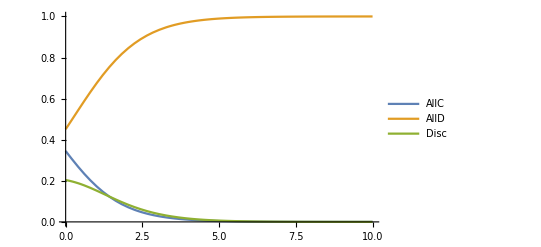

```mathematica
(* Plot numerical solutions *)
ϵ=0.45;
γ=1;
r=3;
Px=r*(x[t]+(1-x[t]-y[t])*gx[t])-1;
Py=r*(x[t]+(1-x[t]-y[t])*gy[t]);
Pz=r*(x[t]+(1-x[t]-y[t])*gz[t])-g;
Pbar=x[t]*Px+y[t]*Py+(1-x[t]-y[t])*Pz;
Δgx=gxgood-gxbad/.{gx->gx[t]};
Δgy=gygood-gybad/.{gy->gy[t]};
Δgz=gzgood-gzbad/.{gz->gz[t]};
g=x[t]*gx[t]+y[t]*gy[t]+(1-x[t]-y[t])*gz[t];
r1=RandomReal[];
r2=RandomReal[];
r3=RandomReal[];
x0=r1/(r1+r2+r3);
y0=r2/(r1+r2+r3);
gx0=RandomReal[];
gy0=RandomReal[];
gz0=RandomReal[];
sol=NDSolve[{x'[t]==x[t]*(Px-Pbar),y'[t]==y[t]*(Py-Pbar),gx'[t]== γ*Δgx,gy'[t]==γ*Δgy,gz'[t]==γ*Δgz,x[0]==x0,y[0]==y0,gx[0]==gx0,gy[0]==gy0,gz[0]== gz0},{x,y,gx,gy,gz},{t,0,200}];
Plot[Evaluate[{x[t],y[t],1-x[t]-y[t]}/.sol],{t,0,10},PlotLegends->{"AllC","AllD","Disc"}]
```